```mathematica
complex variables functions
Lihong Ao
2019271014
SZU,physics
```

```mathematica
第一章
```

```mathematica
(1/2+(√3 ⅈ)/2)^100+(1/2-(√3 ⅈ)/2)^100=ⅇ^(-ⅈ (100π)/3)+ⅇ^(-ⅈ (500π)/3)=ⅇ^(-(2 ⅈ π)/3)+ⅇ^(-(4 ⅈ π)/3)=(-1/2+(√3 ⅈ)/2)+(-1/2-(√3 ⅈ)/2)=-1
-1,0,1,π,-1
```

```mathematica
ⅈ^10-4 ⅈ^15+ⅈ=-1-4 (-ⅈ)+ⅈ=-1-5ⅈ
-1,5,√26,π+ArcTan 5,-1+5ⅈ
```

```mathematica
θ=arg(-6-4ⅈ)=π+ArcTan 2/3
-6-4ⅈ=Cos θ+ⅈ Sin θ=-4/(√13)-ⅈ 9/(√13)=-2 √13 ⅇ^(ⅈ ArcTan[2/3])
```

```mathematica
-√3+ⅈ=Cos (5π)/6+ⅈ Sin (5π)/6=ⅇ^(-ⅈ(5π)/6)
```

```mathematica
((1+ⅈ)/(1-ⅈ))^8=((1+ⅈ)^2/2)^8=1
(√3+ⅈ)^4=(2 ⅇ^(-ⅈ π/6))^4=16 ⅇ^(-ⅈ (2π)/3)=-8+8 √3 ⅈ
(-1)^(1/6)=ⅇ^(ⅈ π/6)=ⅈ/2+(√3)/2
(1-ⅈ)^(1/3)=2^(1/6)ⅇ^((-ⅈ π)/12)=2^(-4/3)(1+√3)+2^(-1/3)(1+√3)ⅈ
```

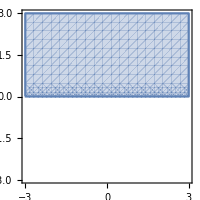

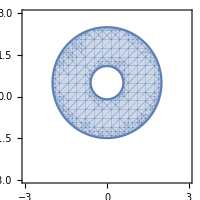

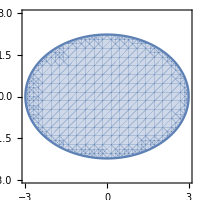

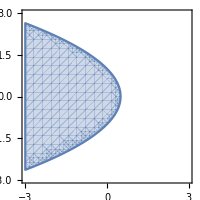

```mathematica
RegionPlot[y>0,{x,-3,3},{y,-3,3},ImageSize->200]
RegionPlot[1.2<√((2x)^2+(2y-1)^2)≤4,{x,-3,3},{y,-3,3},ImageSize->200]
RegionPlot[√((x-2)^2+y^2)+√((x+2)^2+y^2)≤6,{x,-3,3},{y,-3,3},ImageSize->200]
RegionPlot[√(x^2+y^2)+x≤1,{x,-3,3},{y,-3,3},ImageSize->200]
```

```mathematica
w=1/z=1/(x+i y)=(x-i y)/(x^2+y^2)   u=x/(x^2+y^2)=x/3,v=-y/(x^2+y^2)=-y/3    u^2+v^2=1/9
u=x/(x^2+y^2)=x/(2 x^2),v=-y/(x^2+y^2)=x/(2 x^2)     u-v=0
```

```mathematica
f(z)=f(x,y)=1/(2i)((x^2-y^2)-(x^2+y^2))/((x-i y)(x+i y))=(i y^2)/(x^2+y^2)
y=k x     lim_(y=k x ,x->0) f(x,y)=(i k^2 x^2)/((1+k^2)x^2)=(i k^2)/(1+k^2)≠const
```

```mathematica
第二章
```

```mathematica
f(z)=x^2+2y i
(∂u)/(∂x)=2x,(∂v)/(∂y)=2,(∂u)/(∂y)=0,-(∂v)/(∂x)=0
f(z)=z|z|^2
(∂u)/(∂x)=(2 x^2+y^2)/(√(x^2+y^2)),(∂v)/(∂y)=(x^2+2 y^2)/(√(x^2+y^2)),(∂u)/(∂y)=(x y)/(√(x^2+y^2)),-(∂v)/(∂x)=-(x y)/(√(x^2+y^2))
2 x^2+y^2=x^2+2 y^2,x y=-x y ->x=y=0
```

```mathematica
f(z)=(z+1)/(z^2-1)
(∂u)/(∂x)=(1-x^2+y^2)/(((-1+x)^2+y^2)^2),(∂v)/(∂y)=-((-1+x)^2-y^2)/(((-1+x)^2+y^2)^2),(∂u)/(∂y)=-(2 x y)/(((-1+x)^2+y^2)^2),-(∂v)/(∂x)=(-2 (-1+x) y)/(((-1+x)^2+y^2)^2)
1-x^2+y^2=(-1+x)^2-y^2,-2 (-1+x) y=2 x y
{x,y}ϵ∅
```

```mathematica
f(z)=z/(z^2+1)
(∂u)/(∂x)=-(2 x (x^4-2 x^2 (-1+y^2)+(1+y^2)^2))/((1+x^4-6 y^2+y^4-2 x^2 (-1+y^2))^2),(∂v)/(∂y)=-(2 x (1+x^4+6 y^2-3 y^4+2 x^2 (1+y^2)))/((1+x^4-6 y^2+y^4-2 x^2 (-1+y^2))^2),(∂u)/(∂y)=(2 y (5+x^4-2 y^2+y^4-2 x^2 (-3+y^2)))/((1+x^4-6 y^2+y^4-2 x^2 (-1+y^2))^2),-(∂v)/(∂x)=(2 y (1-3 x^4-6 y^2+y^4+2 x^2 (-1+y^2)))/((1+x^4-6 y^2+y^4-2 x^2 (-1+y^2))^2)
2 x (x^4-2 x^2 (-1+y^2)+(1+y^2)^2)==-2 x (1+x^4+6 y^2-3 y^4+2 x^2 (1+y^2)),2 y (5+x^4-2 y^2+y^4-2 x^2 (-3+y^2))==2 y (1-3 x^4-6 y^2+y^4+2 x^2 (-1+y^2))
{x,y}ϵ∅
```

```mathematica
f(z)=x^2+a x y+b y^2+i(c x^2+d x y+y^2)
(∂u)/(∂x)=2 x+a y,(∂v)/(∂y)=d x+2 y,(∂u)/(∂y)=a x+2 b y,-(∂v)/(∂x)=-2 c x-d y
a=2,b=-1,c=-1,d=2
```

```mathematica
f(z)=u+i v=const->u,v=const->OverBar[f(z)]=u-iv=const
(∂u)/(∂x)=(∂(-v))/(∂y),(∂u)/(∂y)=-(∂(-v))/(∂x)

(∂u)/(∂x)=(∂v)/(∂y),(∂u)/(∂y)=-(∂v)/(∂x)
(∂v)/(∂y)=(∂u)/(∂x)=(∂u)/(∂y)=(∂v)/(∂x)=0->f(z)=const
```

```mathematica
z^3+1=0->z=(-1)^(1/3)=ⅇ^(1/3 Ln(-1))=ⅇ^(1/3(π+2k π)i)(k∈ℤ)
ⅇ^x-1=0 ->x=Ln 1=ln 1+2 k π i=2 k π i(k∈ℤ)
Sin z=(ⅇ^(i z)-ⅇ^(-i z))/(2 i)=0    ⅇ^(2i z)=1->z=(Ln 1)/(2 i)=k π(k∈ℤ)
Sin z-Cos z=(ⅇ^(i z)-ⅇ^(-i z))/(2 i)-(ⅇ^(i z)+ⅇ^(-i z))/2=(-1/2-ⅈ/2) ⅇ^(-ⅈ z) (-ⅈ+ⅇ^(2 ⅈ z))=0 
(-1/2-i/2)ⅇ^(-i z)≠0->-i+ⅇ^(2 i z)=0->z=(Ln i)/(2i)=(ln 1+(π/2+2k π)i)/(2 i)=π/4+k π(k∈ℤ)
```

```mathematica
Ln Subscript[z, 1] Subscript[z, 2]=Ln Subscript[z, 1]+Ln Subscript[z, 2]->Ln z^2=Ln z+Ln z,Ln z^3=Ln z^2+Ln z=3 Ln z,Ln z^n=Ln z^(n-1)+Ln z=n Ln z
->Ln z^n=n Ln z
z^n=(Cos θ+i Sin θ)^n=(Cos(θ+2k π)+i Sin(θ+2kπ))^n->Ln z^(1/n)≠1/n Ln z
```

```mathematica
ⅇ^(2+i π)=ⅇ^2(Cos π+i Sin π)=-ⅇ^2
(1+i)^(1-i)=ⅇ^((1-i)Ln(1+i))=ⅇ^((1-i)(ln √2+(π/4+2k π)i))=ⅇ^(Log[2]/2-i/4 ((-1+i) (1+8 k) π+Log[4]))
Ln(3+4i)=ln 5+i(ArcTan 4/3+2k π)
```

```mathematica
ⅇ^z=ⅇ^x(Cos y+i Sin y)     ⅇ^z>0,Re(ⅇ^z)=|ⅇ^z|
Ln z=ln|z|+i Arc z  z≠0    {x,y|x,y∈ℂ,x>0}  1/z
z^b=ⅇ^(b  Ln z)   b∈ℤ->z^b=ⅇ^(b ln z)(唯一值);b=p/q(p,q互质,q>0)->z^b=ⅇ^(p/q ln|z|+i(p/q Arc z))(有限多值);b∉ℚ（无限多值）    b z^(b-1)
Cos z=(ⅇ^(i z)+ⅇ^(-i z))/2    Cos z=Cos(-z),Cos z=Cos(z+2k π)     -Sin z
Sin z=(ⅇ^(i z)-ⅇ^(-i z))/(2i)   Sin z=-Sin(-z),Sin z=Sin(z+2k π)    Cos z
Tan z=(ⅇ^(i z)-ⅇ^(-i z))/(i ⅇ^(i z)+i ⅇ^(-i z))    Tan z=-Tan(-z),Tan z=Tan(z+2k π)    Cot z
Ch z=(ⅇ^z+ⅇ^-z)/2       Ch z=Ch(-z)    Sh z
Sh z=(ⅇ^z-ⅇ^-z)/(2i)     Sh z=-Sh(-z)     Ch z
Th z=(ⅇ^z-ⅇ^-z)/(i(ⅇ^z+ⅇ^-z))   Th z=-Th(-z)  Sech z
```